# Лабораторная работа №4.

## Задание 1.

Создайте интерактивную панель для ввода пользователем концов двух отрезков с помощью мыши. Отобразите отрезки  красным цветом, если они пересекаются и зелёным в противном случае.

```mathematica
DynamicModule[{pointlist={}},Column[{Button["Refresh",pointlist={}],ClickPane[Framed@Dynamic@Graphics[{PointSize@0.02,Point/@pointlist,Black,Line/@Partition[pointlist,2]},PlotRange->{{0,10},{0,10}},ImageSize->500],AppendTo[pointlist,#]&]}]]
```

```mathematica
(*Решение и ход работы*)
lineEq[pt1_,pt2_]:=With[{vect=pt2-pt1},{(x-pt1[[1]])vect[[2]]-vect[[1]](y-pt1[[2]])}]
```

```mathematica
p1={0,0};
p2={2,1};
p3={-1,-3};
p4={0,2};
```

```mathematica
l1=lineEq[p1,p2]
l2=lineEq[p3,p4]
```

{x-2 y}

{-3+5 (1+x)-y}

```mathematica
Solve[l1==0&&l2==0,{x,y}]
```

{{x→-4/9,y→-2/9}}

```mathematica
(*Точка пересечения двух прямых*)
getCommonPt[pt1_,pt2_,pt3_,pt4_]:=Block[{answer=Solve[lineEq[pt1,pt2]==0&&lineEq[pt3,pt4]==0,{x,y}]},Return[{x,y}/.answer[[1]]]]
```

```mathematica
(*Пробую считать расстояние*)
N[Norm[getCommonPt[{-2,0},{0,2},{0,0},{2,4}]-p2]+Norm[getCommonPt[{-2,0},{0,2},{0,0},{2,4}]-p3]]
```

10.6158

```mathematica
(*Принадлежит ли точка отрезку*)
sectorPointQ[pt1_,pt2_,cpt_]:=If[And[N[Norm[pt2-pt1]]==N[Norm[cpt-pt1]+Norm[cpt-pt2]]],True,False]
```

```mathematica
(*Пересекаются ли отрезки*)
segmentsIntersectQ[pt1_,pt2_,pt3_,pt4_]:=Block[{cpt=getCommonPt[pt1,pt2,pt3,pt4]},Return[sectorPointQ[pt1,pt2,cpt]&&sectorPointQ [pt3,pt4,cpt]]]
```

```mathematica
(*Проверяю*)
sectorPointQ[{-2,0},{0,2},{2,4}]
segmentsIntersectQ[{-2,0},{0,2},{0,0},{2,4}]
```

False

False

```mathematica
(*Partition - разделяет список на непересекающиеся подсписки длины n.*)
DynamicModule[{pointlist={}},Column[{Button["Refresh",pointlist={}],ClickPane[Framed@Dynamic@Graphics[{PointSize@0.02,Black,If[Length[pointlist]==4,If[segmentsIntersectQ[Partition[pointlist,2][[1,1]],Partition[pointlist,2][[1,2]],Partition[pointlist,2][[2,1]],Partition[pointlist,2][[2,2]]],Red,Green],Nothing],Point/@pointlist,Line/@Partition[pointlist,2]},PlotRange->{{0,10},{0,10}},ImageSize->500],If[Length[pointlist]<4,AppendTo[pointlist,#],Nothing]&]}]]
(*Всегда иcпользовать Block лучше для наших задач*)
```

## Задание 2.

Создайте функцию, генерирующую итерации ковра серпинского. Фрактал задавайте списком точек. Отобразите точки на графической области.
Обеспечьте возможность просматривать накопление точек с помощью функции Manipulate или анимации.

```mathematica
base={{0,0},{0,1},{1,0},{1,1},{1/2,0},{1/2,1},{1,1/2},{0,1/2}}
```

{{0,0},{0,1},{1,0},{1,1},{1/2,0},{1/2,1},{1,1/2},{0,1/2}}

```mathematica
kover[base_,1]:=Flatten[{base,((base/3) [[#]]+{0,0/3})&/@Range[1,Length[base]],
((base/3) [[#]]+({0,1/3}))&/@Range[1,Length[base]],
((base/3) [[#]]+{0,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{1/3,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{1/3,0})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,0})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,1/3})&/@Range[1,Length[base]]},1]
kover[base_,n_]:=kover[Flatten[{base,((base/3) [[#]]+{0,0/3})&/@Range[1,Length[base]],
((base/3) [[#]]+({0,1/3}))&/@Range[1,Length[base]],
((base/3) [[#]]+{0,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{1/3,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,2/3})&/@Range[1,Length[base]],
((base/3) [[#]]+{1/3,0})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,0})&/@Range[1,Length[base]],
((base/3) [[#]]+{2/3,1/3})&/@Range[1,Length[base]]},1],n-1]
```

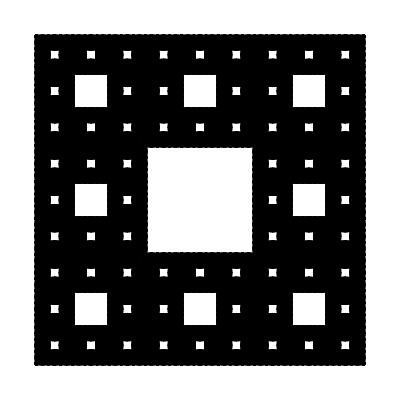

```mathematica
Graphics[{Point[kover[base,4]]}]
```

```mathematica
Manipulate[Graphics[Point[kover[base,a]]],{a,{1,2,3,4}}]
```

```mathematica
getPoint[points_]:=Block[{rNum=RandomInteger[{1,8}]},{(points[[Length[points],1]]+2*base[[rNum,1]])/3,(points[[Length[points],2]]+2*base[[rNum,2]])/3}]
```

```mathematica
pts={{1,1}}
```

{{1,1}}

{{1,1},{1,1/3},{1,1/9},{1/3,1/27},{1/9,1/81},{1/27,82/243},{55/81,568/729},{217/243,2026/2187},{703/729,6400/6561},{703/2187,12961/19683},{2890/6561,52327/59049},{9451/19683,52327/177147},{9451/59049,406621/531441},{127549/177147,1469503/1594323},{481843/531441,3063826/4782969},{1544725/1594323,3063826/14348907},{1544725/4782969,31761640/43046721},{1544725/14348907,31761640/129140163},{1544725/43046721,31761640/387420489},{87638167/129140163,806602618/1162261467},{87638167/387420489,806602618/3486784401},{862479145/1162261467,4293387019/10460353203},{862479145/3486784401,4293387019/31381059609},{4349263546/10460353203,67055506237/94143178827}}

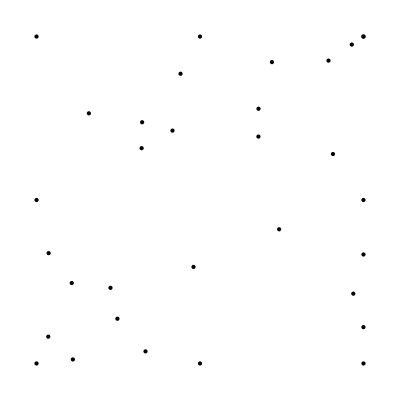

```mathematica
AppendTo[pts,getPoint[pts]]
Graphics[{Point[base],Point[pts]}]
```

## Задание 3

1. Создайте игру, позволяющую пользователю бродить по сетке “целых точек” (точек с целыми координатами) в некоторой графической области. отобразите траекторию и количество сделанных шагов. Управление перемещением точки осуществляется с помощью кнопок. Предусмотрите невозможность выйти за пределы области, а также невозможность пересечения траектории. Предусмотрие кнопку для рестарта игры.
	2. Добавьте на поле специальную область (чёрный квадрат), после попадания в которую игра прекращается. Пользователь получает сообщение. И происходит рестарт.

```mathematica
DynamicModule[{pointlist={{10,10}},a=True},
Grid[
{
{Button["Up",AppendTo[pointlist,Last[pointlist]+{0,1}]],Button["Down",AppendTo[pointlist,Last[pointlist]+{0,-1}]]},{Button["left",AppendTo[pointlist,Last[pointlist]+{-1,0}]],Button["rigth",AppendTo[pointlist,Last[pointlist]+{1,0}]]},
{Dynamic@Graphics[
{Red,PointSize[0.02],Point[pointlist⟦-1⟧],Dashed,,Black,Line[pointlist]},
ImageSize->300,GridLines->{Range[1,20],Range[1,20]},GridLinesStyle->LightGray,Axes->True,PlotRange->{{0,20},{0,20}}
],SpanFromLeft}
},
ItemSize->{Scaled[0.15]}]]
```